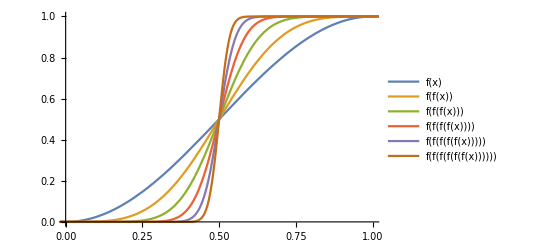

```mathematica
f=(Sin[π #1-π/2]+1)/2&;
fs=Table[Nest[f,x,n],{n,1,6}];
Plot[
fs,
{x,-π,π},PlotRange->{{0,1},{0,1}},
PlotLegends->Table[Nest["f",x,n],{n,1,6}]
]
```